```mathematica
Clear[f]
```

```mathematica
Vfene[r_, ϵ_, r0_, Δ_] := - (ϵ/2) Log[1 - ((r -r0)/Δ)^2];
Vmorse[x_, ϵ_, x0_, a_] := ϵ (1-Exp[ - a ( x - x0)])^2;
Vharm[r_, k_, r0_] := (k / 2) (r - r0)^2;
Vlj[r_, ϵ_, σ_] := 4 ϵ ( (σ/r)^12 - (σ/r)^6);
Vmod[θ_,a_,θ0_] := 1 - a(θ-θ0)^2;
Vsmooth[x_, b_, xc_] := b ( x-xc)^2;
```

```mathematica
dVmoddr[rr_, kk_, rr00_]:=Evaluate[D[Vmod[rr,kk,rr00],rr]];
dVsdr[xx_,bb_,xxcc_] := Evaluate[D[Vsmooth[xx,bb,xxcc],xx]];
```

```mathematica
a=2.; t0=π-0.6; ts=0.65;
```

```mathematica
myVar=FindRoot[ {
Evaluate[Vmod[t0-ts,a,t0]]==Vsmooth[t0-ts,b,t0-tc],
dVmoddr[t0-ts,a,t0]== dVsdr[t0-ts,b,t0-tc]
}, {{b,10}, {tc,10}}, MaxIterations-> 20000];
blow=Abs[b/.myVar];
c=Abs[tc/.myVar];
AccountingForm[blow]
AccountingForm[c]
```

10.9032

0.769231

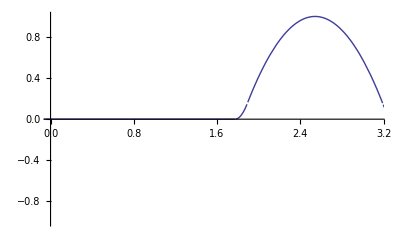

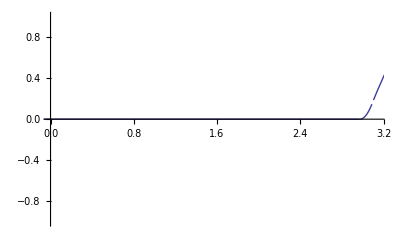

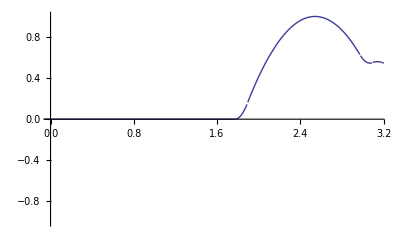

```mathematica
f4[θ_] :=   Piecewise[{
{0,θ<t0-c},
{Vsmooth[θ,blow,t0-c],t0-c<θ<t0-ts},
{Vmod[θ,a,t0] ,t0-ts<θ<t0+ts},
{Vsmooth[θ,blow,t0+c],t0-ts<θ<t0+c},
{0, θ>t0+c}
}]
Plot[f4[x], {x, -2π,2π}, PlotRange->{{0,π},{-1,1}}]
Plot[f4[2π-x], {x, -2π,2π}, PlotRange->{{0,π},{-1,1}}]
Plot[f4[x]+f4[2π-x], {x, -2π,2π}, PlotRange->{{0,π},{-1,1}}]
```

```mathematica
x0=0.5; a=2;
Theta[x_]:=ArcCos[x];
Vmod[x_]:=1-a(x-x0)^2
Theta'[x]
Vmod'[x]
Plot[Vmod'[x]/Sin[x], {x,0,1},PlotRange->{{0,1},{-2π,2π}}];
Plot[Vmod[Theta[x]],{x,0,1}
Plot[-2a (ArcCos[x])/Sin[x],{x,0,1},PlotRange->{{-1,1},{-10π,2π}}];
```

-1/(√(1-x^2))

-4 (-0.5+x)